# Full Lagrangian of ALP-meson interactions

## Generate the Lagrangian or import it

```mathematica
lagrfilename="Lagrangian-ALP-total";
If[!IfκInv,lagrfilename=lagrfilename<>"-No-kappa-inv"];
If[!IfPheavy,lagrfilename=lagrfilename<>"-No-P-heavy"];
lagrfilename=lagrfilename<>".mx"
fLagr=FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology",lagrfilename}];
ifExists=FileExistsQ[fLagr];
If[ifExists,
genlagropt=dropdownDialog[{"Generate","Import"},"Generate the total ALP-meson interaction Lagrangian from scratch, or import the precomputed one (if no changes in the interactions are made)?"];
genlagropt=(genlagropt=="Generate")
,
infoDialog["The Lagrangian for the ALPs has not been generated yet. Generating (takes a few minutes)..."];
genlagropt=True
]
```

Lagrangian-ALP-total.mx

True

## Various interactions with ALPs

## Pure ChPT

```mathematica
If[genlagropt,
LpureChPTalp=ChPTkineticTerm+ChPTbreakingTerm;
LpureChPTalp=LpureChPTalp/.rulem0aTransformationSymbolic;
LpureChPTalp=ruleϵδ[LpureChPTalp];
tabCrossCheck={{"P1","P2","L_(P1P2, mass)","L_(P1P2, kinetic)"}};
quadrpart=ruleLeavingPower[LpureChPTalp,2];
Do[
Module[{val1,val2},
xxx=1/2 D[quadrpart,PfieldSymbol[f1,x],PfieldSymbol[f2,x]];
xxx=xxx/.ruleFieldsToZero/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]//Expand;
val1=xxx/.{δ^2->0}//Simplify;
xxx=1/2 D[quadrpart,dPfieldSymbol[f1,x,μ],dPfieldSymbol[f2,x,μ]];
xxx=xxx/.ruleFieldsToZero/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]//Expand;
val2=xxx/.{δ^2->0}//Simplify;
tabCrossCheck=Join[tabCrossCheck,{{f1,f2,val1,val2}}]
]
,{f1,listMesonP0a},{f2,listMesonP0a}];
tabCrossCheck=tabCrossCheck/.{md->mdsol["η"]}//ruleLeadingOrderIsospin//Simplify;
Print[tabCrossCheck/.{-4 mη^2+mηpr^2+3 mπ0^2->-Simplify[4m2ChPTminimal["η"]-m2ChPTminimal["η'"]-3m2ChPTminimal["π^0"]]}//Simplify];
LpureChPTalp=LpureChPTalp-quadrpart+1/2 Sum[dPfieldSymbol[P,x,μ]*dPfieldSymbol[findingConjugated[P],x,μ]-msymbolic[P]^2 PfieldSymbol[P,x]*PfieldSymbol[findingConjugated[P],x],{P,listMesonP}]//Expand;
LagrangianWithALP["ChPT"]=LpureChPTalp;
]
```

(P1 | P2 | L_(P1P2, mass) | L_(P1P2, kinetic)
a | a | -ma^2/2 | 1/2
a | π^0 | 0 | 0
a | η | 0 | 0
a | η' | 0 | 0
π^0 | a | 0 | 0
π^0 | π^0 | -mπ0^2/2 | 1/2
π^0 | η | 0 | 0
π^0 | η' | 0 | 0
η | a | 0 | 0
η | π^0 | 0 | 0
η | η | -mη^2/2 | 1/2
η | η' | 0 | 0
η' | a | 0 | 0
η' | π^0 | 0 | 0
η' | η | 0 | 0
η' | η' | -mηpr^2/2 | 1/2)

## s->d operator

```mathematica
If[genlagropt,
WeakDecaysTermALP=G8*fπ^4*ruleLeavingPower[Tr[(IdentityMatrix[3]+ChiralRotationCoefficientHC*alp[x]).λmatrix.(IdentityMatrix[3]+ChiralRotationCoefficient*alp[x]).DΣ4alpcqCovariantHC[x,μ].DΣ4alpcqCovariant[x,μ]],4];
WeakDecaysTermALP=(WeakDecaysTermALP/.{ϵ->0})+(D[WeakDecaysTermALP,ϵ]/.{ϵ->0})*ϵ//Expand;
WeakDecaysTermALP=WeakDecaysTermALP+Conjugate[WeakDecaysTermALP]//Expand;
WeakDecaysTermALP=WeakDecaysTermALP/.rulem0aTransformationSymbolic//Expand;
WeakDecaysTermALP=ruleϵδ[WeakDecaysTermALP];
LagrangianWithALP["s→d"]=WeakDecaysTermALP;
]//AbsoluteTiming
```

{1.5×10^-6,Null}

## VMD Lagrangian

```mathematica
If[genlagropt,
(*Expression from https://arxiv.org/pdf/1111.5949.pdf for Subscript[c, 3] = Subscript[c, 1]-Subscript[c, 2] = 1 extended with ALPs*)
(*Note: here, both P and dP are replaced with P, dP explicitly including the Subscript[c, q]-dependent term. This is because they originate from the covariant objects Subscript[D, μ] Subscript[ξ, L], Subscript[D, μ] Subscript[ξ, R] used to obtain Lagrangian, with Σ = (ξ^+)_L Subscript[ξ, R]. And both Subscript[D, μ] Subscript[ξ, L/R] include Subscript[d, μ] a. See https://arxiv.org/pdf/2406.11948 for detail*)
VMDtermALP1=ruleLeadingOrderIsospin[(gVVP*EPSILON[μ,ν,α,β]*2*Tr[PmatrixALPcqCovariant[x].dVmatrix[x,μ,ν].dVmatrix[x,α,β]]+3/(240 Pi^2 fπ^5)(1-15/8)EPSILON[μ,ν,α,β]*2^5 Tr[PmatrixALPcqCovariant[x].dPmatrixALPcqCovariant[x,μ].dPmatrixALPcqCovariant[x,ν].dPmatrixALPcqCovariant[x,α].dPmatrixALPcqCovariant[x,β]])];
VMDtermALP1=(VMDtermALP1/.ϵ->0)+(D[VMDtermALP1,ϵ]/.{ϵ->0})*ϵ//Expand;
VMDtermALP2=ruleLeadingOrderIsospin[cvmd*UnitStep[mηpr-ma]/(2 fπ^2)*Tr[(PmatrixALPcqCovariant[x].dPmatrixALPcqCovariant[x,μ]-dPmatrixALPcqCovariant[x,μ].PmatrixALPcqCovariant[x]).(dPmatrixALPcqCovariant[x,μ].PmatrixALPcqCovariant[x]-PmatrixALPcqCovariant[x].dPmatrixALPcqCovariant[x,μ])]-I*2*gval*Tr[Vmatrix[x,μ].(PmatrixALPcqCovariant[x].dPmatrixALPcqCovariant[x,μ]-dPmatrixALPcqCovariant[x,μ].PmatrixALPcqCovariant[x])]];
VMDtermALP2=(VMDtermALP2/.ϵ->0)+(D[VMDtermALP2,ϵ]/.{ϵ->0})*ϵ//Expand;
VMDtermALP=((VMDtermALP1+VMDtermALP2)/.{ρ0[x,μ_]:>ρ0[x,μ]+VA["ρ^0"]*A[x,μ],dρ0[x,μ_,ν_]:>dρ0[x,μ,ν]+VA["ρ^0"]*dA[x,μ,ν],ϕ[x,μ_]:>ϕ[x,μ]+VA["ϕ"]*A[x,μ],dϕ[x,μ_,ν_]:>dϕ[x,μ,ν]+VA["ϕ"]*dA[x,μ,ν],ω[x,μ_]:>ω[x,μ]+VA["ω"]*A[x,μ],dω[x,μ_,ν_]:>dω[x,μ,ν]+VA["ω"]*dA[x,μ,ν]}//Expand)+LmassKineticVMD;
VMDtermALP=VMDtermALP/.rulem0aTransformationSymbolic//Expand;
VMDtermALP=ruleϵδ[VMDtermALP];
LagrangianWithALP["VMD"]=VMDtermALP;
]//AbsoluteTiming
Conjugate[coef1]^:=coef1;
```

{178.389,Null}

## Light scalar mesons

```mathematica
If[genlagropt,
LscalarAalp=CoefA*(2*Tr[Smatrix[x].dPmatrixALPcqCovariant[x,μ].dPmatrixALPcqCovariant[x,μ]]-Tr[Smatrix[x]]*Tr[dPmatrixALPcqCovariant[x,μ].dPmatrixALPcqCovariant[x,μ]]-2*Tr[Smatrix[x].dPmatrixALPcqCovariant[x,μ]]*Simplify[Tr[dPmatrixALPcqCovariant[x,μ]]]+Tr[Smatrix[x]]*Simplify[Tr[dPmatrixALPcqCovariant[x,μ]]]*Simplify[Tr[dPmatrixALPcqCovariant[x,μ]]]);
LscalarBalp=CoefB*Tr[Smatrix[x]]*Tr[dPmatrixALPcqCovariant[x,μ].dPmatrixALPcqCovariant[x,μ]];
LscalarCalp=CoefC*Tr[Smatrix[x].dPmatrixALPcqCovariant[x,μ]]*Tr[dPmatrixALPcqCovariant[x,μ]]//Expand//Simplify;
LscalarDalp=CoefD*Tr[Smatrix[x]]*Tr[dPmatrixALPcqCovariant[x,μ]]*Tr[dPmatrixALPcqCovariant[x,μ]]//Expand//Simplify;
{LscalarAalp,LscalarBalp,LscalarCalp,LscalarDalp}=((#/.{ϵ->0})+(D[#,ϵ]/.{ϵ->0})ϵ//Expand//Simplify//Expand)&/@{LscalarAalp,LscalarBalp,LscalarCalp,LscalarDalp};
LscalarALP=LscalarAalp+LscalarBalp+LscalarCalp+LscalarDalp;
LscalarALP=LscalarALP/.rulem0aTransformationSymbolic//Expand;
LscalarALP=ruleϵδ[LscalarALP];
LagrangianWithALP["S"]=LscalarALP;
]//AbsoluteTiming
```

{29.9489,Null}

### Alternative form

-Graphics-

```mathematica
(*Mspurion=DiagonalMatrix[{1,1,ms/mu}];
PμΣ[x_,μ_]=I/2(Σ1alp[x].DΣ1alpHC[x,μ]-Σ1alpHC[x].DΣ1alp[x,μ]);
LscalarAlt1=-b/2Tr[Smatrix[x].Smatrix[x].(Σ1alpHC[x].Mspurion.Σ1alpHC[x]+Σ1alp[x].Mspurion.Σ1alp[x])]-d/2 Tr[Smatrix[x]]*Tr[Smatrix[x].(Σ1alpHC[x].Mspurion.Σ1alpHC[x]+Σ1alp[x].Mspurion.Σ1alp[x])]+fπ^2/4*(CoefB*Tr[Smatrix[x]]*Tr[PμΣ[x,μ].PμΣ[x,μ]]+CoefC*Tr[Smatrix[x].PμΣ[x,μ]]*Tr[PμΣ[x,μ]]+CoefD*Tr[Smatrix[x]]*Tr[PμΣ[x,μ]]*Tr[PμΣ[x,μ]]);
LscalarAlt1=ruleϵδ[LscalarAlt1];
LscalarAlt1=LscalarAlt1/.rulem0aTransformationSymbolic//Expand;
LscalarAlt1=ruleϵδ[LscalarAlt1];
LscalarAlt1=(LscalarAlt1//Expand)/.repsIndividual;
LscalarALP2=(LscalarALP//Expand)/.repsIndividual;
expr1=LagrangianGivenFields2[LscalarAlt1,{"a","σ","η"},{1,1,1}]//Simplify
expr2=LagrangianGivenFields2[LscalarALP2,{"a","σ","η"},{1,1,1}]/.{CoefA->0}//Simplify
expr1=expr1/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{δ->0};
expr2=expr2/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{δ->0};
(D[expr1,cG]/.{κu->0,κd->0}//Simplify)/(D[expr2,cG]/.{κu->0,κd->0}//Simplify)//Simplify*)
```

```mathematica
(*expr11=LagrangianGivenFields2[LscalarAlt1,{"a","σ","η"},{1,1,1}]/.{δ->0}//Simplify
expr11=expr11/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/. {κu->0,κd->0}/.{δ->0,cu->0,cd->0,cs->0}//Simplify
ruleSymbolsToNumbersFinal[expr11,0]/.{ma->1.6}*)
(*expr22=expr11/.{cG->0}//Simplify;
expr22=expr22/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/. {κu->κmatrixStandardmdrepl[[1]][[1]],κd->κmatrixStandardmdrepl[[2]][[2]]}/.{δ->0,cu->0,cd->0,cs->0}//Simplify
ruleSymbolsToNumbersFinal[expr22,0]/.{ma->1.6}*)
```

## Tensor mesons

```mathematica
If[genlagropt,
(*So far, only Subscript[f, 2] PP terms. From A.26 of 2110.10691*)
(*Similar to 2110.10691 and 1811.03474, only the first order expansion of Σ in terms of P is used*)
LagrangianTalp=-gT*fπ^2/4(2*TfieldSymbol["f_2",x,μ,ν]*Tr[DiagonalMatrix[{1/2,1/2,0}].(DΣ1ALPcqCovariantHC[x,μ].DΣ1ALPcqCovariant[x,ν]-1/2*mt[μ,ν]*DΣ1ALPcqCovariantHC[x,α].DΣ1ALPcqCovariant[x,α])]);
LagrangianTalp=(LagrangianTalp/.{ϵ->0})+(D[LagrangianTalp,ϵ]/.{ϵ->0})*ϵ//Expand//Simplify;
LagrangianTalp=LagrangianTalp/.rulem0aTransformationSymbolic//Expand;
LagrangianTalp=ruleϵδ[LagrangianTalp];
LagrangianWithALP["T"]=LagrangianTalp;
]
(*LagrangianTalp=-gT*fπ^2/4(2/(√2)*Tr[Tmatrix[x,μ,ν].(DΣ1alpHC[x,μ].DΣ1alp[x,ν]-1/2*mt[μ,ν]*DΣ1alpHC[x,α].DΣ1alp[x,α])]);
LagrangianTalp=(LagrangianTalp/.{ϵ->0})+(D[LagrangianTalp,ϵ]/.{ϵ->0})*ϵ//Expand;*)
```

## Axial-vector and pseudovector mesons

```mathematica
LagrangianVAalp=I*aVA*Tr[VAmatrix1[x,μ].(Vmatrix[x,μ].PmatrixALP[x]-PmatrixALP[x].Vmatrix[x,μ])]+bVA*Tr[VAmatrix2[x,μ].(Vmatrix[x,μ].PmatrixALP[x]+PmatrixALP[x].Vmatrix[x,μ])]//Expand;
LagrangianVAalp=LagrangianVAalp+Conjugate[LagrangianVAalp];
```

## Axial-vector and pseudovector mesons - new (following 1208.0585)

### Definitions

```mathematica
Lmatrix[x_,μ_]=Vmatrix[x,μ]+VAmatrix1[x,μ];
Rmatrix[x_,μ_]=Vmatrix[x,μ]-VAmatrix1[x,μ];
dLmatrix[x_,μ_,ν_]=dVmatrix[x,μ,ν]+dVAmatrix1[x,μ,ν]-dVmatrix[x,ν,μ]-dVAmatrix1[x,ν,μ];
dRmatrix[x_,μ_,ν_]=dVmatrix[x,μ,ν]-dVAmatrix1[x,μ,ν]-dVmatrix[x,ν,μ]+dVAmatrix1[x,ν,μ];
Vμνmatrix[x_,μ_,ν_]=dVmatrix[x,μ,ν]-dVmatrix[x,ν,μ];
```

### Calculating the mixing between axial-vector and pseudoscalar mesons

```mathematica
(*Lagrangian including the mixing between VA mesons and pseudoscalar mesons. The - term removes the PPVV terms and PPV terms, to ensure the absence of double counting (they are already present in the V lagrangian above)*)
LagrangianVAalpForMixing=Tr[ConjugateTranspose[(I*dPmatrixALPcqCovariant[x,μ]-I*g1*(Lmatrix[x,μ].Φmatrix[x]-Φmatrix[x].Rmatrix[x,μ]))].(I*dPmatrixALPcqCovariant[x,μ]-I*g1*(Lmatrix[x,μ].Φmatrix[x]-Φmatrix[x].Rmatrix[x,μ]))]//Expand;
LagrangianVAalpForMixing=LagrangianVAalpForMixing-(LagrangianVAalpForMixing/.Flatten[Table[{VAfieldSymbol[f,x,a_]:>0,dVAfieldSymbol[f,x,a_,b_]:>0},{f,listMesonVA}]]);
LagrangianVAalpForMixing=LagrangianVAalpForMixing/.rulem0aTransformationSymbolic;
LagrangianVAalpForMixing=(LagrangianVAalpForMixing/.ϵ->0)+(D[LagrangianVAalpForMixing,ϵ]/.{ϵ->0})*ϵ;
LagrangianVAalp1=Expand[LagrangianVAalpForMixing]/. repsIndividual;
LagrangianGivenFieldsVA[fieldlist_,powerlist_]:=Block[{},
Total[Cases[LagrangianVAalp1,t^(Sum[y[fieldlist[[i]]]*powerlist[[i]],{i,1,Length[fieldlist]}])*aa_:>aa]]
]
(*Removing quadratic terms from the initial integration*)
LagrangianVAalpForMixing=LagrangianVAalpForMixing-ruleLeavingPower[LagrangianVAalpForMixing,2]//Expand;
(*Renormalization constants Subscript[Z, P] required to preserve the kinetic terms of pseudoscalar mesons after the shift Subscript[A, μ] -> Subscript[A, μ] + c Subscript[d, μ] P. See Eqs. (10)-(14) of 1208.0585*)
ZP["π^0"]=ZP["π^+"]=ZP["π^-"]=ma1/(√(ma1^2-g1^2*ϕN^2));
ZP["a"] = 1;
soltemp=Solve[{c1*1/(√6)+c2 1/(2 √3)==ma1/(√(ma1^2-g1^2*ϕN^2)),c1*1/(√3)-c2 1/(√6)==mf11420/(√(mf11420^2-2 g1^2*ϕS^2))},{c1,c2}][[1]]//Simplify;
{ZP["η"],ZP["η'"]}={c1/.soltemp,c2/.soltemp};
ZP["K^+"]=ZP["K^-"]=ZP["K_L"]=ZP["K_S"]=(2*mK11270)/(√(4 mK11270^2-g1^2(ϕN+√2 ϕS)^2));
Do[
MVAP0[VA,findingConjugated[P]]=LagrangianGivenFieldsVA[{P,VA},{1,1}]/(VAfieldSymbol[VA,x,μ]*dPfieldSymbol[P,x,μ])/.{ϵ->1}//Simplify;
(*Mixing angles. Defined via Eqs. (10)-(14) of 1208.0585. Note the appearance of the renormalization constants Subscript[Z, P]. Perfect isospin limit is assumed*)
θVAP[VA,findingConjugated[P]]=MVAP0[VA,findingConjugated[P]]*If[P=="a",(1-msymbolic[findingConjugated[P]]^2/msymbolic[VA]^2)/(msymbolic[findingConjugated[P]]^2-msymbolic[VA]^2-I*Γsymbolic[VA]*msymbolic[VA]),ZP[P]/msymbolic[VA]^2]/.{δ->0}//Simplify;
,{P,listMesonP},{VA,listMesonVA}];
(*Symbolic diagonalization*)
ruleVAmixingRepl=Flatten[Table[VAfieldSymbol[VA,x,μ]->VAfieldSymbol[VA,x,μ]+VAmix*Sum[If[!NumericQ[θVAP[VA,P0]],If[P0=="a",ϵ,1]*θVAPsym[VA,P0]*dPfieldSymbol[P0,x,μ],0],{P0,listMesonP}],{VA,listMesonVA}]];
ruleθVAP0explicit=Flatten[Table[θVAPsym[VA,P0]->θVAP[VA,P0],{VA,listMesonVA},{P0,listMesonP}],1];
(*Renormalized matrix*)
PmatrixALPrenormalized[x_]=I*PmatrixALP[x]/.Table[PfieldSymbol[f,x]->ZP[f]*PfieldSymbol[f,x],{f,listMesonP}];
PmatrixALPrenormalizedHC[x_]=-I*PmatrixALPHC[x]/.Table[PfieldSymbol[f,x]->ZP[f]*PfieldSymbol[f,x],{f,listMesonP}];
ΦmatrixRenormalized[x_]=SheavyMatrixCondensate[x]+PmatrixALPrenormalized[x];
ΦmatrixRenormalizedHC[x_]=SheavyMatrixCondensate[x]+PmatrixALPrenormalizedHC[x];
```

### Full interaction

```mathematica
If[genlagropt,
(*Full interactions involving VA, V, and pseudoscalars. The pure V part (no VA) is deducted. No interactions with photons are included, as they are irrelevant*)
LagrangianVAalp=h2*(Tr[Lmatrix[x,μ].ΦmatrixRenormalized[x].ΦmatrixRenormalizedHC[x].Lmatrix[x,μ]+Rmatrix[x,μ].ΦmatrixRenormalized[x].ΦmatrixRenormalizedHC[x].Rmatrix[x,μ]])+2*h3*Tr[Lmatrix[x,μ].ΦmatrixRenormalized[x].Rmatrix[x,μ].ΦmatrixRenormalizedHC[x]]+I*g2/2*(Tr[dLmatrix[x,μ,ν].(Lmatrix[x,μ].Lmatrix[x,ν]-Lmatrix[x,ν].Lmatrix[x,μ])]+Tr[dRmatrix[x,μ,ν].(Rmatrix[x,μ].Rmatrix[x,ν]-Rmatrix[x,ν].Rmatrix[x,μ])])//Expand;
(*Going to the mass basis in the sector of light pseudoscalar mesons*)
LagrangianVAalp=LagrangianVAalp/.rulem0aTransformationSymbolic//Expand;
(*Summing the kinetic term and the term added above*)
LagrangianVAalp=LagrangianVAalp+LagrangianVAalpForMixing;
(*Dropping O(δ^2) terms*)
LagrangianVAalp=(LagrangianVAalp/.{ϵ->0})+(D[LagrangianVAalp,ϵ]/.{ϵ->0})*ϵ;
(*Dropping O(ϵ^2) terms*)
LagrangianVAalp=(LagrangianVAalp/.{δ->0})+δ*(D[LagrangianVAalp,δ]/.{δ->0});
(*Removing the terms that do not include at least one axial-vector field*)
LagrangianVAalp=LagrangianVAalp-(LagrangianVAalp/.Flatten[Table[{VAfieldSymbol[f,x,a_]:>0,dVAfieldSymbol[f,x,a_,b_]:>0},{f,listMesonVA}]])//Expand;
(*Shifting the axial-vector fields by the mixing angle*)
LagrangianVAalp=LagrangianVAalp/.ruleVAmixingRepl;
(*Removing the terms being higher than linear in the mixing between AV and P mesons*)
LagrangianVAalp=(LagrangianVAalp/.{VAmix->0})+(D[LagrangianVAalp,VAmix]/.{VAmix->0});
(*Dropping the quadratic terms*)
LagrangianVAalp=LagrangianVAalp-ruleLeavingPower[LagrangianVAalp,2]//Expand;
LagrangianWithALP["VA"]=coefVA*LagrangianVAalp;
]//AbsoluteTiming
```

{13.878,Null}

```mathematica
{#,θVAP[#,"a"],D[θVAP[#,"a"]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription],cG]//Simplify}&/@listMesonVA
```

((K^+)_1(1270) | 0 | 0
(K^-)_1(1270) | 0 | 0
(K^0)_1(1270) | 0 | 0
((K̄)^0)_1(1270) | 0 | 0
(K^+)_1(1400) | 0 | 0
(K^-)_1(1400) | 0 | 0
(K^0)_1(1400) | 0 | 0
((K̄)^0)_1(1400) | 0 | 0
(a^+)_1 | 0 | 0
(a^-)_1 | 0 | 0
(a^0)_1 | (g1 ϕN (1-ma^2/ma1^2) (cd+cG κd-cG κu-cu-π0ALP))/(ma^2-ma1 (ma1+ⅈ Γa1)) | (δ g1 mπ0^2 ϕN (ma1^2-ma^2) (ma^2 (2 mη^2+mηpr^2-3 mπ0^2)+mη^2 (mπ0^2-3 mηpr^2)+2 mηpr^2 mπ0^2))/(3 ma1^2 (ma^2-mη^2) (ma^2-mηpr^2) (ma^2-mπ0^2) (-ma^2+ma1 (ma1+ⅈ Γa1)))
(b^+)_1 | 0 | 0
(b^-)_1 | 0 | 0
(b^0)_1 | 0 | 0
f_1(1285) | -(g1 ϕN (1-ma^2/mf11285^2) (3 cd+3 cG κd+3 cG κu+3 cu+√6 ηALP+√3 ηprALP))/(3 (ma^2-mf11285 (mf11285+ⅈ Γf11285))) | (g1 ϕN (ma^2-mf11285^2) (ma^2 (2 mη^2+mηpr^2-3 mπ0^2)+mη^2 (mπ0^2-3 mηpr^2)+2 mηpr^2 mπ0^2))/(3 mf11285^2 (ma^2-mη^2) (ma^2-mηpr^2) (-ma^2+mf11285 (mf11285+ⅈ Γf11285)))
f_1(1420) | (g1 ϕS (1-ma^2/mf11420^2) (6 cG (κd+κu-1)-6 cs+√6 ηALP-2 √3 ηprALP))/(3 (ma^2-mf11420 (mf11420+ⅈ Γf11420))) | (2 g1 ϕS (mf11420^2-ma^2) (ma^2-mπ0^2) (mη^2-mηpr^2))/(3 mf11420^2 (ma^2-mη^2) (ma^2-mηpr^2) (-ma^2+mf11420 (mf11420+ⅈ Γf11420)))
h_1(1170) | 0 | 0
h_1(1415) | 0 | 0)

```mathematica
LagrangianVAalp
```

ⅈ aVA cG ϵ alp(x) K10bar1270(x,μ) Kstar0(x,μ)-2 ⅈ aVA cG ϵ κd alp(x) K10bar1270(x,μ) Kstar0(x,μ)-ⅈ aVA cG ϵ κu alp(x) K10bar1270(x,μ) Kstar0(x,μ)+bVA cG ϵ alp(x) K10bar1400(x,μ) Kstar0(x,μ)-bVA cG ϵ κu alp(x) K10bar1400(x,μ) Kstar0(x,μ)-(ⅈ aVA a10(x,μ) KL(x) Kstar0(x,μ))/(2 √2)-(bVA b10(x,μ) KL(x) Kstar0(x,μ))/(2 √2)+(ⅈ aVA f11285(x,μ) KL(x) Kstar0(x,μ))/(2 √2)-1/2 ⅈ aVA f11420(x,μ) KL(x) Kstar0(x,μ)+(bVA h11170(x,μ) KL(x) Kstar0(x,μ))/(2 √2)+1/2 bVA h11415(x,μ) KL(x) Kstar0(x,μ)+(ⅈ aVA a1plus(x,μ) Kminus(x) Kstar0(x,μ))/(√2)+(bVA b1plus(x,μ) Kminus(x) Kstar0(x,μ))/(√2)+(ⅈ aVA a10(x,μ) KS(x) Kstar0(x,μ))/(2 √2)+(bVA b10(x,μ) KS(x) Kstar0(x,μ))/(2 √2)-(ⅈ aVA f11285(x,μ) KS(x) Kstar0(x,μ))/(2 √2)+1/2 ⅈ aVA f11420(x,μ) KS(x) Kstar0(x,μ)-(bVA h11170(x,μ) KS(x) Kstar0(x,μ))/(2 √2)-1/2 bVA h11415(x,μ) KS(x) Kstar0(x,μ)-ⅈ √(2/3) aVA K10bar1270(x,μ) η(x) Kstar0(x,μ)+(ⅈ aVA K10bar1270(x,μ) ηpr(x) Kstar0(x,μ))/(2 √3)+1/2 √3 bVA K10bar1400(x,μ) ηpr(x) Kstar0(x,μ)+1/2 ⅈ aVA K10bar1270(x,μ) π0(x) Kstar0(x,μ)-1/2 bVA K10bar1400(x,μ) π0(x) Kstar0(x,μ)-(ⅈ aVA K1minus1270(x,μ) πplus(x) Kstar0(x,μ))/(√2)+(bVA K1minus1400(x,μ) πplus(x) Kstar0(x,μ))/(√2)-ⅈ aVA cG ϵ alp(x) K101270(x,μ) Kstar0bar(x,μ)+2 ⅈ aVA cG ϵ κd alp(x) K101270(x,μ) Kstar0bar(x,μ)+ⅈ aVA cG ϵ κu alp(x) K101270(x,μ) Kstar0bar(x,μ)+bVA cG ϵ alp(x) K101400(x,μ) Kstar0bar(x,μ)-bVA cG ϵ κu alp(x) K101400(x,μ) Kstar0bar(x,μ)+(ⅈ aVA a10(x,μ) KL(x) Kstar0bar(x,μ))/(2 √2)-(bVA b10(x,μ) KL(x) Kstar0bar(x,μ))/(2 √2)-(ⅈ aVA f11285(x,μ) KL(x) Kstar0bar(x,μ))/(2 √2)+1/2 ⅈ aVA f11420(x,μ) KL(x) Kstar0bar(x,μ)+(bVA h11170(x,μ) KL(x) Kstar0bar(x,μ))/(2 √2)+1/2 bVA h11415(x,μ) KL(x) Kstar0bar(x,μ)-(ⅈ aVA a1minus(x,μ) Kplus(x) Kstar0bar(x,μ))/(√2)+(bVA b1minus(x,μ) Kplus(x) Kstar0bar(x,μ))/(√2)+(ⅈ aVA a10(x,μ) KS(x) Kstar0bar(x,μ))/(2 √2)-(bVA b10(x,μ) KS(x) Kstar0bar(x,μ))/(2 √2)-(ⅈ aVA f11285(x,μ) KS(x) Kstar0bar(x,μ))/(2 √2)+1/2 ⅈ aVA f11420(x,μ) KS(x) Kstar0bar(x,μ)+(bVA h11170(x,μ) KS(x) Kstar0bar(x,μ))/(2 √2)+1/2 bVA h11415(x,μ) KS(x) Kstar0bar(x,μ)-ⅈ aVA cG ϵ alp(x) K1plus1270(x,μ) Kstarminus(x,μ)+ⅈ aVA cG ϵ κd alp(x) K1plus1270(x,μ) Kstarminus(x,μ)+2 ⅈ aVA cG ϵ κu alp(x) K1plus1270(x,μ) Kstarminus(x,μ)+bVA cG ϵ alp(x) K1plus1400(x,μ) Kstarminus(x,μ)-bVA cG ϵ κd alp(x) K1plus1400(x,μ) Kstarminus(x,μ)-1/2 ⅈ aVA a1plus(x,μ) KL(x) Kstarminus(x,μ)+1/2 bVA b1plus(x,μ) KL(x) Kstarminus(x,μ)-1/2 ⅈ aVA a10(x,μ) Kplus(x) Kstarminus(x,μ)+1/2 bVA b10(x,μ) Kplus(x) Kstarminus(x,μ)-1/2 ⅈ aVA f11285(x,μ) Kplus(x) Kstarminus(x,μ)+(ⅈ aVA f11420(x,μ) Kplus(x) Kstarminus(x,μ))/(√2)+1/2 bVA h11170(x,μ) Kplus(x) Kstarminus(x,μ)+(bVA h11415(x,μ) Kplus(x) Kstarminus(x,μ))/(√2)-1/2 ⅈ aVA a1plus(x,μ) KS(x) Kstarminus(x,μ)+1/2 bVA b1plus(x,μ) KS(x) Kstarminus(x,μ)+ⅈ aVA cG ϵ alp(x) K1minus1270(x,μ) Kstarplus(x,μ)-ⅈ aVA cG ϵ κd alp(x) K1minus1270(x,μ) Kstarplus(x,μ)-2 ⅈ aVA cG ϵ κu alp(x) K1minus1270(x,μ) Kstarplus(x,μ)+bVA cG ϵ alp(x) K1minus1400(x,μ) Kstarplus(x,μ)-bVA cG ϵ κd alp(x) K1minus1400(x,μ) Kstarplus(x,μ)+1/2 ⅈ aVA a1minus(x,μ) KL(x) Kstarplus(x,μ)+1/2 bVA b1minus(x,μ) KL(x) Kstarplus(x,μ)+1/2 ⅈ aVA a10(x,μ) Kminus(x) Kstarplus(x,μ)+1/2 bVA b10(x,μ) Kminus(x) Kstarplus(x,μ)+1/2 ⅈ aVA f11285(x,μ) Kminus(x) Kstarplus(x,μ)-(ⅈ aVA f11420(x,μ) Kminus(x) Kstarplus(x,μ))/(√2)+1/2 bVA h11170(x,μ) Kminus(x) Kstarplus(x,μ)+(bVA h11415(x,μ) Kminus(x) Kstarplus(x,μ))/(√2)-1/2 ⅈ aVA a1minus(x,μ) KS(x) Kstarplus(x,μ)-1/2 bVA b1minus(x,μ) KS(x) Kstarplus(x,μ)+ⅈ √(2/3) aVA K101270(x,μ) Kstar0bar(x,μ) η(x)+ⅈ √(2/3) aVA K1plus1270(x,μ) Kstarminus(x,μ) η(x)-ⅈ √(2/3) aVA K1minus1270(x,μ) Kstarplus(x,μ) η(x)-(ⅈ aVA K101270(x,μ) Kstar0bar(x,μ) ηpr(x))/(2 √3)+1/2 √3 bVA K101400(x,μ) Kstar0bar(x,μ) ηpr(x)-(ⅈ aVA K1plus1270(x,μ) Kstarminus(x,μ) ηpr(x))/(2 √3)+1/2 √3 bVA K1plus1400(x,μ) Kstarminus(x,μ) ηpr(x)+(ⅈ aVA K1minus1270(x,μ) Kstarplus(x,μ) ηpr(x))/(2 √3)+1/2 √3 bVA K1minus1400(x,μ) Kstarplus(x,μ) ηpr(x)-1/2 ⅈ aVA K101270(x,μ) Kstar0bar(x,μ) π0(x)-1/2 bVA K101400(x,μ) Kstar0bar(x,μ) π0(x)+1/2 ⅈ aVA K1plus1270(x,μ) Kstarminus(x,μ) π0(x)+1/2 bVA K1plus1400(x,μ) Kstarminus(x,μ) π0(x)-1/2 ⅈ aVA K1minus1270(x,μ) Kstarplus(x,μ) π0(x)+1/2 bVA K1minus1400(x,μ) Kstarplus(x,μ) π0(x)+(ⅈ aVA K1plus1270(x,μ) Kstar0bar(x,μ) πminus(x))/(√2)+(bVA K1plus1400(x,μ) Kstar0bar(x,μ) πminus(x))/(√2)-(ⅈ aVA K10bar1270(x,μ) Kstarplus(x,μ) πminus(x))/(√2)+(bVA K10bar1400(x,μ) Kstarplus(x,μ) πminus(x))/(√2)+(ⅈ aVA K101270(x,μ) Kstarminus(x,μ) πplus(x))/(√2)+(bVA K101400(x,μ) Kstarminus(x,μ) πplus(x))/(√2)+bVA cG ϵ κd alp(x) b10(x,μ) ρ0(x,μ)+bVA cG ϵ κu alp(x) b10(x,μ) ρ0(x,μ)-bVA cG ϵ κd alp(x) h11170(x,μ) ρ0(x,μ)+bVA cG ϵ κu alp(x) h11170(x,μ) ρ0(x,μ)+(ⅈ aVA K101270(x,μ) KL(x) ρ0(x,μ))/(2 √2)-(bVA K101400(x,μ) KL(x) ρ0(x,μ))/(2 √2)-(ⅈ aVA K10bar1270(x,μ) KL(x) ρ0(x,μ))/(2 √2)-(bVA K10bar1400(x,μ) KL(x) ρ0(x,μ))/(2 √2)-1/2 ⅈ aVA K1plus1270(x,μ) Kminus(x) ρ0(x,μ)+1/2 bVA K1plus1400(x,μ) Kminus(x) ρ0(x,μ)+1/2 ⅈ aVA K1minus1270(x,μ) Kplus(x) ρ0(x,μ)+1/2 bVA K1minus1400(x,μ) Kplus(x) ρ0(x,μ)-(ⅈ aVA K101270(x,μ) KS(x) ρ0(x,μ))/(2 √2)+(bVA K101400(x,μ) KS(x) ρ0(x,μ))/(2 √2)-(ⅈ aVA K10bar1270(x,μ) KS(x) ρ0(x,μ))/(2 √2)-(bVA K10bar1400(x,μ) KS(x) ρ0(x,μ))/(2 √2)+√(2/3) bVA b10(x,μ) η(x) ρ0(x,μ)+(bVA b10(x,μ) ηpr(x) ρ0(x,μ))/(√3)+bVA h11170(x,μ) π0(x) ρ0(x,μ)-ⅈ aVA a1plus(x,μ) πminus(x) ρ0(x,μ)+ⅈ aVA a1minus(x,μ) πplus(x) ρ0(x,μ)-ⅈ aVA cG ϵ κd a1plus(x,μ) alp(x) ρminus(x,μ)+ⅈ aVA cG ϵ κu a1plus(x,μ) alp(x) ρminus(x,μ)+bVA cG ϵ κd alp(x) b1plus(x,μ) ρminus(x,μ)+bVA cG ϵ κu alp(x) b1plus(x,μ) ρminus(x,μ)-1/2 ⅈ aVA K1plus1270(x,μ) KL(x) ρminus(x,μ)+1/2 bVA K1plus1400(x,μ) KL(x) ρminus(x,μ)+(ⅈ aVA K10bar1270(x,μ) Kplus(x) ρminus(x,μ))/(√2)+(bVA K10bar1400(x,μ) Kplus(x) ρminus(x,μ))/(√2)+1/2 ⅈ aVA K1plus1270(x,μ) KS(x) ρminus(x,μ)-1/2 bVA K1plus1400(x,μ) KS(x) ρminus(x,μ)+√(2/3) bVA b1plus(x,μ) η(x) ρminus(x,μ)+(bVA b1plus(x,μ) ηpr(x) ρminus(x,μ))/(√3)+ⅈ aVA a1plus(x,μ) π0(x) ρminus(x,μ)-ⅈ aVA a10(x,μ) πplus(x) ρminus(x,μ)+bVA h11170(x,μ) πplus(x) ρminus(x,μ)+ⅈ aVA cG ϵ κd a1minus(x,μ) alp(x) ρplus(x,μ)-ⅈ aVA cG ϵ κu a1minus(x,μ) alp(x) ρplus(x,μ)+bVA cG ϵ κd alp(x) b1minus(x,μ) ρplus(x,μ)+bVA cG ϵ κu alp(x) b1minus(x,μ) ρplus(x,μ)+1/2 ⅈ aVA K1minus1270(x,μ) KL(x) ρplus(x,μ)+1/2 bVA K1minus1400(x,μ) KL(x) ρplus(x,μ)-(ⅈ aVA K101270(x,μ) Kminus(x) ρplus(x,μ))/(√2)+(bVA K101400(x,μ) Kminus(x) ρplus(x,μ))/(√2)+1/2 ⅈ aVA K1minus1270(x,μ) KS(x) ρplus(x,μ)+1/2 bVA K1minus1400(x,μ) KS(x) ρplus(x,μ)+√(2/3) bVA b1minus(x,μ) η(x) ρplus(x,μ)+(bVA b1minus(x,μ) ηpr(x) ρplus(x,μ))/(√3)-ⅈ aVA a1minus(x,μ) π0(x) ρplus(x,μ)+ⅈ aVA a10(x,μ) πminus(x) ρplus(x,μ)+bVA h11170(x,μ) πminus(x) ρplus(x,μ)+2 bVA cG ϵ alp(x) h11415(x,μ) ϕ(x,μ)-2 bVA cG ϵ κd alp(x) h11415(x,μ) ϕ(x,μ)-2 bVA cG ϵ κu alp(x) h11415(x,μ) ϕ(x,μ)+1/2 ⅈ aVA K101270(x,μ) KL(x) ϕ(x,μ)+1/2 bVA K101400(x,μ) KL(x) ϕ(x,μ)-1/2 ⅈ aVA K10bar1270(x,μ) KL(x) ϕ(x,μ)+1/2 bVA K10bar1400(x,μ) KL(x) ϕ(x,μ)+(ⅈ aVA K1plus1270(x,μ) Kminus(x) ϕ(x,μ))/(√2)+(bVA K1plus1400(x,μ) Kminus(x) ϕ(x,μ))/(√2)-(ⅈ aVA K1minus1270(x,μ) Kplus(x) ϕ(x,μ))/(√2)+(bVA K1minus1400(x,μ) Kplus(x) ϕ(x,μ))/(√2)-1/2 ⅈ aVA K101270(x,μ) KS(x) ϕ(x,μ)-1/2 bVA K101400(x,μ) KS(x) ϕ(x,μ)-1/2 ⅈ aVA K10bar1270(x,μ) KS(x) ϕ(x,μ)+1/2 bVA K10bar1400(x,μ) KS(x) ϕ(x,μ)-√(2/3) bVA h11415(x,μ) η(x) ϕ(x,μ)+(2 bVA h11415(x,μ) ηpr(x) ϕ(x,μ))/(√3)-bVA cG ϵ κd alp(x) b10(x,μ) ω(x,μ)+bVA cG ϵ κu alp(x) b10(x,μ) ω(x,μ)+bVA cG ϵ κd alp(x) h11170(x,μ) ω(x,μ)+bVA cG ϵ κu alp(x) h11170(x,μ) ω(x,μ)-(ⅈ aVA K101270(x,μ) KL(x) ω(x,μ))/(2 √2)+(bVA K101400(x,μ) KL(x) ω(x,μ))/(2 √2)+(ⅈ aVA K10bar1270(x,μ) KL(x) ω(x,μ))/(2 √2)+(bVA K10bar1400(x,μ) KL(x) ω(x,μ))/(2 √2)-1/2 ⅈ aVA K1plus1270(x,μ) Kminus(x) ω(x,μ)+1/2 bVA K1plus1400(x,μ) Kminus(x) ω(x,μ)+1/2 ⅈ aVA K1minus1270(x,μ) Kplus(x) ω(x,μ)+1/2 bVA K1minus1400(x,μ) Kplus(x) ω(x,μ)+(ⅈ aVA K101270(x,μ) KS(x) ω(x,μ))/(2 √2)-(bVA K101400(x,μ) KS(x) ω(x,μ))/(2 √2)+(ⅈ aVA K10bar1270(x,μ) KS(x) ω(x,μ))/(2 √2)+(bVA K10bar1400(x,μ) KS(x) ω(x,μ))/(2 √2)+√(2/3) bVA h11170(x,μ) η(x) ω(x,μ)+(bVA h11170(x,μ) ηpr(x) ω(x,μ))/(√3)+bVA b10(x,μ) π0(x) ω(x,μ)+bVA b1plus(x,μ) πminus(x) ω(x,μ)+bVA b1minus(x,μ) πplus(x) ω(x,μ)

```mathematica
expr=LagrangianGivenFields[{"π^0","(b^0)_1","ω"},{1,1,1}];//AbsoluteTiming
```

{0.089182,Null}

```mathematica
Do[
expr=Sum[LagrangianGivenFields1[LagrangianVAalp,{P,"(b^0)_1",V},{1,1,1}]/.{VfieldSymbol[V,x,μ]->VA[V]*A[x,μ]},{V,{"ρ^0","ϕ","ω"}}];
Print[Row[{P,": ",expr}]]
,{P,listMesonP0a}]
```

a: (4 √(2 π) √αEM bVA cG fπ κd ϵ alp(x) A(x,μ) b10(x,μ))/(3 mρplus)+(8 √(2 π) √αEM bVA cG fπ κu ϵ alp(x) A(x,μ) b10(x,μ))/(3 mρplus)

π^0: (2 √(2 π) √αEM bVA fπ π0(x) A(x,μ) b10(x,μ))/(3 mρplus)

η: (4 √(π/3) √αEM bVA fπ η(x) A(x,μ) b10(x,μ))/mρplus

η': (2 √((2 π)/3) √αEM bVA fπ ηpr(x) A(x,μ) b10(x,μ))/mρplus

```mathematica
Do[
expr=Sum[LagrangianGivenFields1[LagrangianVAalp,{P,"h_1(1170)",V},{1,1,1}]/.{VfieldSymbol[V,x,μ]->VA[V]*A[x,μ]},{V,{"ρ^0","ϕ","ω"}}];
Print[Row[{P,": ",expr}]]
,{P,listMesonP0a}]
```

a: (8 √(2 π) √αEM bVA cG fπ κu ϵ alp(x) A(x,μ) h11170(x,μ))/(3 mρplus)-(4 √(2 π) √αEM bVA cG fπ κd ϵ alp(x) A(x,μ) h11170(x,μ))/(3 mρplus)

π^0: (2 √(2 π) √αEM bVA fπ π0(x) A(x,μ) h11170(x,μ))/mρplus

η: (4 √(π/3) √αEM bVA fπ η(x) A(x,μ) h11170(x,μ))/(3 mρplus)

η': (2 √((2 π)/3) √αEM bVA fπ ηpr(x) A(x,μ) h11170(x,μ))/(3 mρplus)

## Pseudoscalar excitations (following 1612.09218; it is connected to 1208.0585)

```mathematica
If[genlagropt,
(*Defining the interactions between excitations and other particles BEFORE shifting axial-vector fields and light pseudoscalar fields*)
LPheavyALPinteraction1=2*h3star*Tr[Lmatrix[x,μ].PheavyMatrixALP[x].Rmatrix[x,μ].ΦmatrixRenormalizedHC[x]+Lmatrix[x,μ].Φmatrix[x].Rmatrix[x,μ].PheavyMatrixALPHC[x]];
LPheavyALPinteraction2=h2star*Tr[PheavyMatrixALPHC[x].Lmatrix[x,μ].Lmatrix[x,μ].ΦmatrixRenormalized[x]+ΦmatrixRenormalizedHC[x].Lmatrix[x,μ].Lmatrix[x,μ].PheavyMatrixALP[x]+Rmatrix[x,μ].PheavyMatrixALPHC[x].ΦmatrixRenormalized[x].Rmatrix[x,μ]+Rmatrix[x,μ].ΦmatrixRenormalizedHC[x].PheavyMatrixALP[x].Rmatrix[x,μ]];
LPheavyALPinteraction=LPheavyALPinteraction1+LPheavyALPinteraction2;
(*Performing diagonalization in the light pseudoscalar sector*)
LPheavyALPinteraction=LPheavyALPinteraction/.rulem0HeavyaTransformationSymbolic;
LPheavyALPinteraction=ruleϵδ[LPheavyALPinteraction];
(*Performing diagonalization in the axial-vector sector due to VA-dP mixing*)
LPheavyALPinteraction=LPheavyALPinteraction/.ruleVAmixingRepl//Expand;
(*Leaving only O(VA-dP mixing^2) terms, to get the decays of the type Subscript[P, excitation]->PPP and Subscript[P, excitation]->PV*)
LPheavyALPinteraction=(LPheavyALPinteraction/.VAmix->0)+(D[LPheavyALPinteraction,VAmix]/.{VAmix->0})+(D[LPheavyALPinteraction,VAmix,VAmix]/2/.{VAmix->0});
LPheavyALPinteraction=ruleϵδ[LPheavyALPinteraction];
(*Adding the quadratic terms*)
LPheavyALPinteraction+=Sum[(dPheavyFieldSymbol[mes,x,μ]*dPheavyFieldSymbol[mes,x,μ])/2-msymbolic[mes]/2 PheavyFieldSymbol[mes,x],{mes,listMesonPheavy}];
LagrangianWithALP["Pheavy"]=coefPheavy*LPheavyALPinteraction;
]//AbsoluteTiming
```

{5.87659,Null}

```mathematica
(*expr11=LagrangianGivenFields1[LPheavyALPinteraction,{"a","K^(*+)","K^-"},{1,1,1}];
expr11=expr11//Simplify
expr11=expr11/.rulem0HeavyaTransformationSymbolicToExplicit/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription];
D[expr11,cG]//Simplify*)
```

```mathematica
(*expr11=LagrangianGivenFields1[LPheavyALPinteraction,{"a","K^+","K_S","π^-"},{1,1,1,1}]//Simplify;
expr11=expr11/.rulem0HeavyaTransformationSymbolicToExplicit;
D[expr11,cu]*cu+D[expr11,cd]*cd+D[expr11,cs]*cs/.{mη1295->mπ01300}//Simplify
D[expr11,cG]*cG//Simplify*)
```

-(ⅈ ϵ (ma^2-mπ0^2) (mη^2-mηpr^2))/(3 √2 (ma^2-mη^2) (ma^2-mηpr^2))

### Effect of unaccounted mixing terms

```mathematica
trace=α*I*Tr[PheavyMatrixHC[x].PmatrixALP[x]-PheavyMatrix[x].PmatrixALPHC[x]]/.rulem0aTransformationSymbolic/.{δ->0};
coeff=D[D[trace,alp[x],η1440[x]]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription],cG]//Simplify
Sum[alp[x]*PheavyFieldSymbol[f,x]*D[trace,alp[x],PheavyFieldSymbol[f,x]]/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{δ->0,cu->0,cd->0,cs->0}//Simplify,{f,listMesonP0heavy}]/.{cG->Subscript[c, G],ma->Subscript[m, a],mη->Subscript[m, η],mηpr->Subscript[m, η'],mπ0->Subscript[m, π]}//TeXForm
```

(√2 α ϵ (ma^2-mπ0^2) (mη^2-mηpr^2))/(3 (ma^2-mη^2) (ma^2-mηpr^2))

\frac{\sqrt{2} \alpha  \epsilon  \left(m_a^2-m_{\pi }^2\right) \text{alp}(x) c_G \text{$\eta $1440}(x) \left(m_{\eta }^2-m_{\eta '}^2\right)}{3 \left(m_a^2-m_{\eta }^2\right) \left(m_a^2-m_{\eta '}^2\right)}-\frac{\alpha  \epsilon  \text{alp}(x)
   c_G \text{$\eta $1295}(x) \left(m_a^2 \left(m_{\eta '}^2+2 m_{\eta }^2-3 m_{\pi }^2\right)+2 m_{\pi }^2 m_{\eta '}^2+m_{\eta }^2 \left(m_{\pi }^2-3 m_{\eta '}^2\right)\right)}{3 \left(m_a^2-m_{\eta }^2\right) \left(m_a^2-m_{\eta '}^2\right)}

## Nucleons

### Relevant Lagrangian

1/(6 fπ)ϵ (n Conjugate[n] dalp(x,μ) (6 cd (DD+DDs+F)+6 cG (DD (-κu)+DD+DDs+F (2 κd+κu-1))+6 cs DD+6 cs DDs-6 cs F+6 cu DDs+3 √3 DD ηprALP-3 DD π0ALP+√6 DDs ηALP+4 √3 DDs ηprALP+2 √6 F ηALP-√3 F ηprALP-3 F π0ALP)+p Conjugate[p] dalp(x,μ) (6 cd DDs+6 cG (DD (-κd)+DD+DDs+F (κd+2 κu-1))+6 cs (DD+DDs-F)+6 cu DD+6 cu DDs+6 cu F+3 √3 DD ηprALP+3 DD π0ALP+√6 DDs ηALP+4 √3 DDs ηprALP+2 √6 F ηALP-√3 F ηprALP+3 F π0ALP))+1/(6 fπ)(Conjugate[p] (p dη(x,μ) (3 δ DD ηπ0+√6 DDs+3 δ F ηπ0+2 √6 F)+3 δ DD ηprπ0 p dηpr(x,μ)+3 √3 DD p dηpr(x,μ)-3 √3 δ DD ηprπ0 p dπ0(x,μ)+3 DD p dπ0(x,μ)+3 √2 DD n dπplus(x,μ)+4 √3 DDs p dηpr(x,μ)-√6 δ DDs ηπ0 p dπ0(x,μ)-4 √3 δ DDs ηprπ0 p dπ0(x,μ)+3 δ F ηprπ0 p dηpr(x,μ)-√3 F p dηpr(x,μ)-2 √6 δ F ηπ0 p dπ0(x,μ)+√3 δ F ηprπ0 p dπ0(x,μ)+3 F p dπ0(x,μ)+3 √2 F n dπplus(x,μ))-Conjugate[n] (n dη(x,μ) (3 δ DD ηπ0-√6 DDs+3 δ F ηπ0-2 √6 F)+3 δ DD ηprπ0 n dηpr(x,μ)-3 √3 DD n dηpr(x,μ)+3 √3 δ DD ηprπ0 n dπ0(x,μ)+3 DD n dπ0(x,μ)-3 √2 DD p dπminus(x,μ)-4 √3 DDs n dηpr(x,μ)+√6 δ DDs ηπ0 n dπ0(x,μ)+4 √3 δ DDs ηprπ0 n dπ0(x,μ)+3 δ F ηprπ0 n dηpr(x,μ)+√3 F n dηpr(x,μ)+2 √6 δ F ηπ0 n dπ0(x,μ)-√3 δ F ηprπ0 n dπ0(x,μ)+3 F n dπ0(x,μ)-3 √2 F p dπminus(x,μ)))

Couplings for ALP = {π^0,η_8,η_0}:

{(2 cd DDs+2 cs DD+2 cs DDs-2 cs F+2 cu DD+2 cu DDs+2 cu F+DD+F)/(2 fπ),(6 cd DDs+6 cs (DD+DDs-F)+6 cu DD+6 cu DDs+6 cu F-√3 DD+3 √3 F)/(6 fπ),(3 DDs (2 cd+2 cs+2 cu+√6)+2 DD (3 cs+3 cu+√6)+6 F (cu-cs))/(6 fπ)}

Couplings for ALP = {π^0,η,η'}:

{(2 cd DDs+2 cs DD+2 cs DDs-2 cs F+2 cu DD+2 cu DDs+2 cu F+DD+F)/(2 fπ),(6 cd DDs+6 cs (DD+DDs-F)+6 cu (DD+DDs+F)+√6 DDs+2 √6 F)/(6 fπ),(DDs (6 cd+6 cs+6 cu+4 √3)+3 DD (2 cs+2 cu+√3)-F (6 cs-6 cu+√3))/(6 fπ)}

dg_aNN/dκ = 0

True

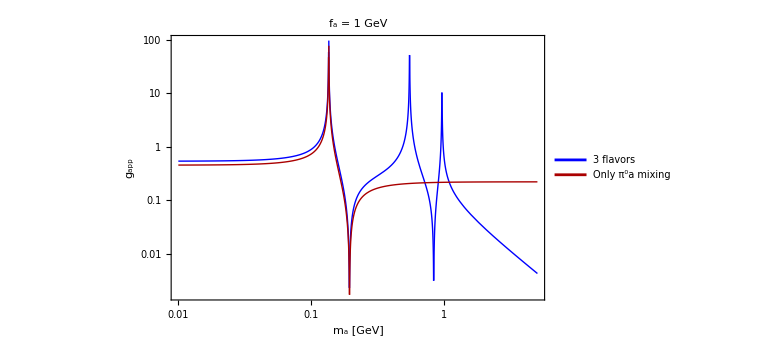

```mathematica
Nmatrix={{0,0,p},{0,0,n},{0,0,0}};
NmatrixBar=ConjugateTranspose[Nmatrix];
lagr1=With[{m=(dPmatrixALPcqCovariant[x,μ]/.rulem0aTransformationSymbolic)},2/fπ(DDs/2 Tr[NmatrixBar.Nmatrix]*Tr[m]+DD/2 Tr[NmatrixBar.(m.Nmatrix+Nmatrix.m)]+F/2 Tr[NmatrixBar.(m.Nmatrix-Nmatrix.m)])//Expand//Simplify];
lagr1=(lagr1/.{ϵ->0})+(D[lagr1,ϵ]/.{ϵ->0})*ϵ
gaNNsymbolic=gappsymbolic=D[lagr1,Conjugate[p],p,dalp[x,μ]];
gannsymbolic=D[lagr1,Conjugate[n],n,dalp[x,μ]];
(*gaNNsymbolic=1/fπ((DDs*κd*cG*ϵ+(DD+DDs-F)(1-κu-κd)*cG*ϵ+cG*ϵ*κu*(DD+DDs+F))+ϵ/2((DD+F)π0ALP-1/(√3)(DD-3F)(eta8/.etasols)+√(2/3)(2DD+3DDs)(eta0/.etasols)))/.{η[x]->ηALP,ηpr[x]->ηprALP}/.replθηηPr//Simplify*)
Print["Couplings for ALP = {π^0,η_8,η_0}:"]
With[{expr=gaNNsymbolic/.{ηALP->ctheta*eta8-stheta*eta0,ηprALP->stheta*eta8+ctheta*eta0}/.replθηηPr/.{cG->0,ϵ->1}},{expr/.{π0ALP->1,eta8->0,eta0->0}//Simplify,expr/.{π0ALP->0,eta8->1,eta0->0}//Simplify,(expr/.{π0ALP->0,eta8->0,eta0->1})//Simplify}]
Print["Couplings for ALP = {π^0,η,η'}:"]
With[{expr=gaNNsymbolic/.{cG->0,ϵ->1}},{expr/.{π0ALP->1,ηALP->0,ηprALP->0}//Simplify,expr/.{π0ALP->0,ηALP->1,ηprALP->0}//Simplify,(expr/.{π0ALP->0,ηALP->0,ηprALP->1})//Simplify}]
test1=gaNNsymbolic/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{cu->0,cd->0,cs->0}//Simplify;
Print["dg_aNN/dκ = 0"]
(D[test1,κu]κu+D[test1,κd]κd/.{mηpr^2->M2relationPureChPT["η'"]}//Simplify) ==0
gaNNexplicit[ma_,cu_,cd_,cs_,cG_,ϵ_]=Simplify[gaNNsymbolic/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{mηpr^2->M2relationPureChPT["η'"]}]/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2}//Expand//Simplify;
gaNNnumeric[ma_,cu_,cd_,cs_,cG_,fa_]=ruleSymbolsToNumbersFinal[gaNNexplicit[ma,cu,cd,cs,cG,ϵ],2]/.{F->0.46,DD->0.8,DDs->-0.41}//Simplify;
tabCouplings[ma_,fa_]=gaNNnumeric[ma,cRGval[#,10^3.,"cu"],cRGval[#,10^3.,"cd"],cRGval[#,10^3.,"cs"],cRGval[#,10^3.,"cG"],fa]&/@{"Fermion universal","Gluon"};
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"auxiliary data/appCouplings.mx"}],{{"ALP-fermion","ALP-gluon"},tabCouplings[ma,Fπ/ϵ]}//Transpose,"MX"];
gaNNexplicit1[ma_,cu_,cd_,cs_,cG_,ϵ_]=Simplify[gaNNsymbolic/.rulem0aTransformationSymbolicToExplicit["Only π^0a"]/.{mηpr^2->M2relationPureChPT["η'"]}]/.{ma^2-4 mη^2+3 mπ0^2->ma^2-mηpr^2}//Expand//Simplify;
gaNNnumericOnlyπ0aMixing[ma_,cu_,cd_,cs_,cG_,fa_]=ruleSymbolsToNumbersFinal[gaNNexplicit1[ma,cu,cd,cs,cG,ϵ]/.{κu->1-κd},2]/.{F->0.46,DD->0.8,DDs->-0.41}//Simplify;
LogLogPlot[{Abs[gaNNnumeric[ma,0,0,0,1,1]],Abs[gaNNnumericOnlyπ0aMixing[ma,0,0,0,1,1]]},{ma,0.01,5},PlotRange->All,ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,20],FrameLabel->{"m_a [GeV]","g_app"},PlotLabel->Style[Row[{"f_a = 1 GeV"}],18,Black],PlotLegends->Placed[Style[#,18]&/@{"3 flavors","Only π^0a mixing"},{0.2,0.8}],PlotStyle->{{Thick,Blue},{Thick,Darker@Red}}]
```

## Constructing full Lagrangian and converting it into a form suitable for scaling

```mathematica
If[genlagropt,
KeysInteractions=Keys[DownValues@LagrangianWithALP][[All,1,1]];
ResourceFunction["MonitorProgress"]@Do[
LagrangianWithALPscaled[int]=Expand[LagrangianWithALP[int]]/.repsIndividual;
,{int,KeysInteractions}];
Export[fLagr,Table[{int,LagrangianWithALPscaled[int]},{int,KeysInteractions}],"MX"];
,
LagrData=Import[fLagr,"MX"];
KeysInteractions=LagrData[[All,1]];
Do[
LagrangianWithALPscaled[LagrData[[i]][[1]]]=LagrData[[i]][[2]];
,{i,1,Length[LagrData],1}]
]
TotalLagrangianScaled=Sum[LagrangianWithALPscaled[int],{int,KeysInteractions}];
Print["Number of terms in the Lagrangian (may be reduced by a factor of few since the symmetry over indices permutations is not included at this step):"]
TotalLagrangianScaled=TotalLagrangianScaled/.{coefVA->0};
TotalLagrangianScaled//Length
LagrangianGivenFields[fieldlist_,powerlist_]:=Block[{},
terms=Total[Cases[TotalLagrangianScaled,t^(Sum[y[fieldlist[[i]]]*powerlist[[i]],{i,1,Length[fieldlist]}])*aa_:>aa]]
]
Print["Example: the Lagrangian including exactly 1 ALP, 1 π^+, 1 π^-, and 1 π^0:"]
expr=LagrangianGivenFields[{"a","π^+","π^-","π^0"},{1,1,1,1}];//AbsoluteTiming
expr//Simplify
```

Number of terms in the Lagrangian (may be reduced by a factor of few since the symmetry over indices permutations is not included at this step):

69879

Example: the Lagrangian including exactly 1 ALP, 1 π^+, 1 π^-, and 1 π^0:

{0.0353752,Null}

1/(18 fπ^2)ϵ (1/(√(ma1^2-g1^2 ϕN^2))alp(x) (3 dπminus(x,μ) (π0(x) dπplus(x,μ) (-3 coefPheavy fπ^2 θVAPsym((a^-)_1,π^-) θVAPsym((a^+)_1,π^+) (cG (κd-κu)-π01300ALP) (h3star (√(ma1^2-g1^2 ϕN^2)+ma1)+2 h2star ma1)+6 cvmd √(ma1^2-g1^2 ϕN^2) mηpr-ma (cG (κu-κd)+π0ALP)-4 π0ALP √(ma1^2-g1^2 ϕN^2))-πplus(x) dπ0(x,μ) (-3 coefPheavy fπ^2 h3star (√(ma1^2-g1^2 ϕN^2)+ma1) θVAPsym((a^0)_1,π^0) θVAPsym((a^-)_1,π^-) (cG (κd-κu)-π01300ALP)+3 cvmd √(ma1^2-g1^2 ϕN^2) mηpr-ma (cG (κu-κd)+π0ALP)-2 π0ALP √(ma1^2-g1^2 ϕN^2)))-πminus(x) (3 dπ0(x,μ) dπplus(x,μ) (-3 coefPheavy fπ^2 h3star (√(ma1^2-g1^2 ϕN^2)+ma1) θVAPsym((a^0)_1,π^0) θVAPsym((a^+)_1,π^+) (cG (κd-κu)-π01300ALP)+3 cvmd √(ma1^2-g1^2 ϕN^2) mηpr-ma (cG (κu-κd)+π0ALP)-2 π0ALP √(ma1^2-g1^2 ϕN^2))+2 mπ0^2 π0(x) πplus(x) √(ma1^2-g1^2 ϕN^2) (δ (3 cG (√6 ηπ0+√3 ηprπ0+1) (κd+κu)+ηALP (6 ηπ0+3 √2 ηprπ0+√6)+ηprALP (3 √2 ηπ0+3 ηprπ0+√3))+3 cG κd-3 cG κu-3 π0ALP)))-3 dalp(x,μ) (πplus(x) (π0(x) dπminus(x,μ)-2 πminus(x) dπ0(x,μ))+π0(x) πminus(x) dπplus(x,μ)) (4 cd-2 (-2 cG κd+2 cG κu+2 cu+π0ALP)+3 cvmd mηpr-ma (cG (κu-κd)+π0ALP)))

```mathematica
listMesonVA
```

{(K^+)_1(1270),(K^-)_1(1270),(K^0)_1(1270),((K̄)^0)_1(1270),(K^+)_1(1400),(K^-)_1(1400),(K^0)_1(1400),((K̄)^0)_1(1400),(a^+)_1,(a^-)_1,(a^0)_1,(b^+)_1,(b^-)_1,(b^0)_1,f_1(1285),f_1(1420),h_1(1170),h_1(1415)}

```mathematica
expr=LagrangianGivenFields[{"π^0","(b^0)_1","ω"},{1,1,1}];//AbsoluteTiming
```

{0.0289174,Null}

```mathematica
expr
```

0